## Images

### Matching Quadratics

#### separate images

```mathematica
lp = ContourPlot3D[x^2 + y^2 + 1 - z, {x, -1, 1}, {y, -1, 1}, {z, -2, 2}, Contours -> 0]
```

-Graphics3D-

```mathematica
fp = ContourPlot3D[Sin[x - 1] Sin[y - 1] - z, {x, -2, 2}, {y, -2, 2}, {z, -2, 2}, Contours -> 0]
```

-Graphics3D-

#### quadratic (parabaloid) that doesn’t match f(x,y) near (0,0)

```mathematica
miss=Show[fp,lp,Graphics3D[{PointSize[Large],Blue,Point[{0,0,Sin[-1]Sin[-1]}]}]]
```

-Graphics3D-

#### separate images

```mathematica
lp2=ContourPlot3D[x y-z,{x,-1,1},{y,-1,1},{z,-1,2},Contours->0]
```

-Graphics3D-

```mathematica
fp2=ContourPlot3D[Sin[x]Sin[y]-z,{x,-2,2},{y,-2,2},{z,-2,2},Contours->0]
```

-Graphics3D-

#### quadratic (parabaloid) that does match f(x,y) near (0,0)

```mathematica
hit=Show[fp2,lp2,Graphics3D[{PointSize[Large],Blue,Point[{0,0,0}]}]]
```

-Graphics3D-

#### paired images

```mathematica
GraphicsRow[{hit,miss}]
```

-Graphics-

### Discretization at t=1/3,2/3

```mathematica
Manipulate[Show[Plot[Piecewise[{{3 x t,t<1/3},{3(y-x)t+2 x-y,1/3<t<2/3},{3(1-y)t+3y-2,t>2/3}}],{t,0,1},Ticks->{{0,0.5,1},Automatic},AxesLabel->{"t","x"},PlotRange->{0,1}],ParametricPlot[{1/3,t},{t,0,x},PlotStyle->{Purple,Dashing[{0.025,0.025}]}],ParametricPlot[{2/3,t},{t,0,y},PlotStyle->{Purple,Dashing[{0.025,0.025}]}]],{{x,0.36},0,1},{{y,0.36},0,1}]
```

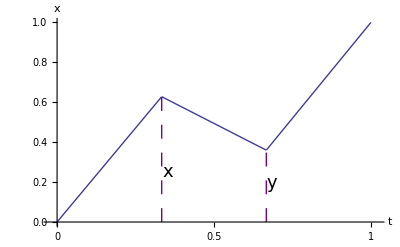

## Contours of Taylor quadratic

```mathematica
Manipulate[GraphicsGrid[{{Show[ContourPlot[1/2*Derivative[2,0][f][a,b](x-a)^2+Derivative[1,1][f][a,b](x-a)(y-b)+1/2*Derivative[0,2][f][a,b](y-b)^2+Derivative[1,0][f][a,b](x-a)+Derivative[0,1][f][a,b](y-b)+f[a,b],{x,-2,2},{y,-2,2},ContourStyle->{{Thick,Red}},ColorFunction->"CherryTones"],cp1],Show[cp,ContourPlot3D[1/2*Derivative[2,0][f][a,b](x-a)^2+Derivative[1,1][f][a,b](x-a)(y-b)+1/2*Derivative[0,2][f][a,b](y-b)^2+Derivative[1,0][f][a,b](x-a)+Derivative[0,1][f][a,b](y-b)+f[a,b]-z,{x,-2,2},{y,-2,2},{z,-6,6},Contours->{0},ContourStyle->{Red,Opacity[.6]}],Graphics3D[{PointSize[Large],Red,Point[{a,b,f[a,b]}]}]]}},ImageSize->Large],{a,-1,1},{{b,-1},-1,1},Initialization :>(to3d[plot_,height_,opacity_]:=Module[{newplot},newplot=First@Graphics[plot];newplot=N@newplot/.{x_?AtomQ,y_?AtomQ}->{x,y,height};
newplot/.GraphicsComplex[xx__]->{Opacity[opacity],GraphicsComplex[xx]}];f[x_,y_]=x^3-2 x y-4 y^2-3 x;
cp=ContourPlot3D[f[x,y]-z,{x,-2,2},{y,-2,2},{z,-6,6},Contours->{0},ContourStyle->Opacity[.3]];
cp1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},ContourShading->False];)]
```